Manipulate that shows the result of a boost (specified by rapidity angle α.)

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/classicalmechanics" ]
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 14]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
r[alpha_] := {{Cosh[alpha], Sinh[alpha]},{Sinh[alpha], Cosh[alpha]}};

c = 1;

Manipulate[
Row[{
ParametricPlot[{c t, g t^2 + v t + x0},{t,0,2}, PlotLabel->Row[{"x = ", g, "t^2 + " , v , "t + ", x0}]
],
ParametricPlot[r[alpha].{c t, g t^2 + v t + x0},{t,0,2}
]
}]

,{{alpha,0,"α"},0,0.5}
,{{g,1,"g"},0,10}
,{{v,1,"v"},0,10}
,{{x0,1,"x_0"},0,10}
]
```

```mathematica
Manipulate[
ParametricPlot[r[alpha].{c t, x},{alpha,0,1},
AxesLabel->{"c t", "x"}],
{{t,1},0,10},
{{x,5},0,10}]
```

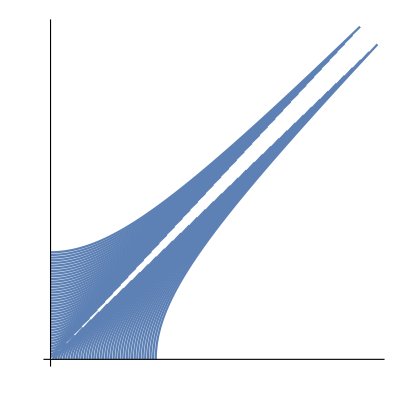

```mathematica
r2[alpha_] := Reverse[r[alpha]];

p = ParametricPlot[ 
Table[rho{r2[alpha].{1,0},r2[alpha].{0,1}},{rho,0,10,0.25}]
,{alpha,0,1.8}
,Ticks->None
,AxesLabel->{MaTeX["x"], MaTeX["ct"]}]
```

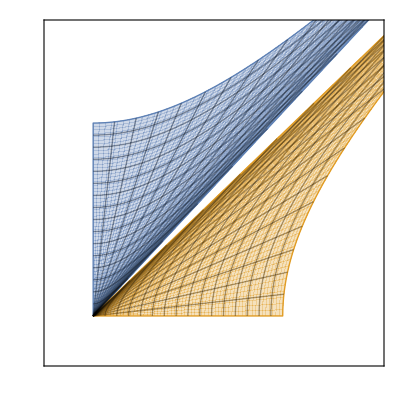

```mathematica
p2 = ParametricPlot[ 
{rho{Sinh[alpha],Cosh[alpha]},rho{Cosh[alpha],Sinh[alpha]}}// Evaluate
,{rho,0,10}
,{alpha,0,1.8}
, FrameTicks-> None
, Axes -> True
,AxesLabel->{MaTeX["x"], MaTeX["ct"]}
, PlotRange -> 1.5{{-1.5,10},{-1.5,10}}
, Mesh ->Automatic
]
```

```mathematica
peeters`exportForLatex["boostsCylindricalFig1", p]
```

```mathematica
peeters`exportForLatex["boostsCylindricalFig1", p2]
```

{boostsCylindricalFig1.eps,boostsCylindricalFig1pn.png}